## Latest attempt

## Values for j=4 (NEW!)

```mathematica
(*J11+J31*)
```

```mathematica
J11=(1-Exp[-x^(-a)])*Integrate[Exp[-y^(-a)]*D[y^(-a*w)Log[y],y],{y,0,x},Assumptions->a>0&&0<w<1&&x>0]
```

((1-ⅇ^(-x^-a)) (Gamma[w,x^-a] (1-a w Log[x])+w MeijerG[{{},{1,1}},{{0,0,w},{}},x^-a]))/a

```mathematica
J31=Exp[-x^(-a)]*Integrate[(1-Exp[-y^(-a)])*D[y^(-a*w)Log[y],y],{y,x,Infinity},Assumptions->a>0&&0<w<1&&x>0]
```

$Aborted

```mathematica
Integrate[(J11+J31)/x//Simplify,{x,0,Infinity},Assumptions->a>0&&0<w<1]
```

Integrate[1/(a x)(Gamma[w,x^-a]-a ⅇ^(-x^-a) x^(-a w) Log[x]-a w Gamma[w,x^-a] Log[x]+w MeijerG[{{},{1,1}},{{0,0,w},{}},x^-a]-ⅇ^(-x^-a) Gamma[w] (1+w PolyGamma[0,w])),{x,0,∞},Assumptions→a>0&&0<w<1]

```mathematica
(*J12+J32*)
```

```mathematica
J12=(1-Exp[-x^(-a)])*Integrate[Exp[-y^(-a)]*D[y^(-a*w),y],{y,0,x},Assumptions->a>0&&x>0&&0<w<1]
```

-((1-ⅇ^(-x^-a)) w Gamma[w,x^-a])

```mathematica
J32=Exp[-x^(-a)]*Integrate[(1-Exp[-y^(-a)])*D[y^(-a*w),y],{y,x,Infinity},Assumptions->a>0&&x>0&&0<w<1]
```

ⅇ^(-x^-a) (-x^(-a w)+w Gamma[w]-w Gamma[w,x^-a])

```mathematica
Integrate[(J12+J32)/x//Simplify,{x,0,Infinity},Assumptions->a>0&&0<w<1]
```

Integrate[ⅇ^(-x^-a) x^(-1-a w) (-1+w x^(a w) Gamma[w]-ⅇ^(x^-a) w x^(a w) Gamma[w,x^-a]),{x,0,∞},Assumptions→a>0&&0<w<1]

```mathematica
(*J13+J33*)
```

```mathematica
J13=(1-Exp[-x^(-a)])*Integrate[Exp[-y^(-a)]*D[Log[y],y],{y,0,x},Assumptions->a>0&&x>0]
```

((1-ⅇ^(-x^-a)) Gamma[0,x^-a])/a

```mathematica
J33=Exp[-x^(-a)]*Integrate[(1-Exp[-y^(-a)])*D[Log[y],y],{y,x,Infinity},Assumptions->a>0&&x>0]
```

(ⅇ^(-x^-a) (EulerGamma-ExpIntegralEi[-x^-a]-a Log[x]))/a

```mathematica
FullSimplify[(J13+J33)/x,Assumptions->a>0&&x>0]
```

(ⅇ^(-x^-a) (EulerGamma-ⅇ^(x^-a) ExpIntegralEi[-x^-a]-a Log[x]))/(a x)

```mathematica
Integrate[(ⅇ^(-x^-a) (EulerGamma-ⅇ^(x^-a) ExpIntegralEi[-x^-a]-a Log[x]))/(a x),{x,0,∞},Assumptions->a>0]
```

π^2/(6 a^2)

### schmier

```mathematica
Integrate[ⅇ^(-x^-a) x^(-1-a w) (-1),{x,0,∞},Assumptions->a>0&&0<w<1]
```

-Gamma[w]/a

```mathematica
Integrate[Exp[-y^(-a)]*y^(-a*w-1)Log[y],{y,0,x},Assumptions->a>0&&0<w<1&&x>0]
```

(a Gamma[w,x^-a] Log[x]-MeijerG[{{},{1,1}},{{0,0,w},{}},x^-a])/a^2

```mathematica
Integrate[(1-Exp[-y^(-a)])*y^(-a*w-1)Log[y],{y,x,Infinity},Assumptions->a>0&&0<w<1&&x>0]
```

1/a^2(a Gamma[w,x^-a] Log[x]+(x^(-a w) (1+a w Log[x]))/w^2-MeijerG[{{},{1,1}},{{0,0,w},{}},x^-a]+Gamma[w] PolyGamma[0,w])

```mathematica
Integrate[(Gamma[w]Exp[-x]- Gamma[w,x])/x,{x,0,∞},Assumptions->a>0&&0<w<1]
```

-Gamma[w] (EulerGamma+PolyGamma[0,w])

```mathematica
Integrate[(Gamma[w]Exp[-x^(-a)]- Gamma[w,x^(-a)])/x,{x,0,∞},Assumptions->a>0&&0<w<1]
```

Integrate[(ⅇ^(-x^-a) Gamma[w]-Gamma[w,x^-a])/x,{x,0,∞},Assumptions→a>0&&0<w<1]

```mathematica
D[Gamma[w,u],w]
```

Gamma[w,u] Log[u]+MeijerG[{{},{1,1}},{{0,0,w},{}},u]

```mathematica
Integrate[(ⅇ^(-x^-a)x^(-a w)(1+Log[x^(a w)]))/x,{x,0,∞},Assumptions->a>0&&0<w<1]
```

(Gamma[w] (1-w PolyGamma[0,w]))/a

```mathematica
Integrate[(ⅇ^-x Gamma[w]PolyGamma[0,w]-D[Gamma[w,x],w])/x,{x,0,∞},Assumptions->0<w<1]
```

-Gamma[w] (PolyGamma[0,w] (EulerGamma+PolyGamma[0,w])+PolyGamma[1,w])

## Values for j=4 (OLD!)

```mathematica
(*J11+J31*)
```

```mathematica
J11=(1-Exp[-x^(-a)])*Integrate[Exp[-y^(-a)]*D[y^(-a)Log[y],y],{y,0,x},Assumptions->a>0]
```

((1-ⅇ^(-x^-a)) (-ExpIntegralEi[-x^-a]+ⅇ^(-x^-a) (1-a Log[x])))/a

```mathematica
J31=Exp[-x^(-a)]*Integrate[(1-Exp[-y^(-a)])*D[y^(-a)Log[y],y],{y,x,Infinity},Assumptions->a>0]
```

(ⅇ^(-x^-a) (-1+ⅇ^(-x^-a)+EulerGamma-ExpIntegralEi[-x^-a]+a (-ⅇ^(-x^-a)-x^-a) Log[x]))/a

```mathematica
Integrate[(J11+J31)/x//Simplify,{x,0,Infinity},Assumptions->a>0]
```

(-6 EulerGamma+π^2)/(6 a^2)

```mathematica
(*J12+J32*)
```

```mathematica
J12=(1-Exp[-x^(-a)])*Integrate[Exp[-y^(-a)]*D[y^(-a),y],{y,0,x},Assumptions->a>0&&x>0]
```

-ⅇ^(-x^-a) (1-ⅇ^(-x^-a))

```mathematica
J32=Exp[-x^(-a)]*Integrate[(1-Exp[-y^(-a)])*D[y^(-a),y],{y,x,Infinity},Assumptions->a>0&&x>0]
```

ⅇ^(-x^-a) (1-ⅇ^(-x^-a)-x^-a)

```mathematica
Integrate[(J12+J32)/x//Simplify,{x,0,Infinity},Assumptions->a>0]
```

-1/a

```mathematica
(*J13+J33*)
```

```mathematica
J13=(1-Exp[-x^(-a)])*Integrate[Exp[-y^(-a)]*D[Log[y],y],{y,0,x},Assumptions->a>0&&x>0]
```

((1-ⅇ^(-x^-a)) Gamma[0,x^-a])/a

```mathematica
J33=Exp[-x^(-a)]*Integrate[(1-Exp[-y^(-a)])*D[Log[y],y],{y,x,Infinity},Assumptions->a>0&&x>0]
```

(ⅇ^(-x^-a) (EulerGamma-ExpIntegralEi[-x^-a]-a Log[x]))/a

```mathematica
FullSimplify[(J13+J33)/x,Assumptions->a>0&&x>0]
```

(ⅇ^(-x^-a) (EulerGamma-ⅇ^(x^-a) ExpIntegralEi[-x^-a]-a Log[x]))/(a x)

```mathematica
Integrate[(ⅇ^(-x^-a) (EulerGamma-ⅇ^(x^-a) ExpIntegralEi[-x^-a]-a Log[x]))/(a x),{x,0,∞},Assumptions->a>0]
```

π^2/(6 a^2)

## Values \sigma_{i,j} for i,j<4

```mathematica
cdfY[y_,a_,p0_]:=Exp[-y^(-a)]*(1+p0*y^(-a))(*Piecewise[{{Exp[-y^(-a)]*(a+p0*y^(-a)),y>0},{0,y<=0}}]*)
```

```mathematica
pdfY[y_,a_,p0_]:=D[cdfY[y,a,p0],y]
```

```mathematica
pdfY[y,a,p0]
```

-a ⅇ^(-y^-a) p0 y^(-1-a)+a ⅇ^(-y^-a) y^(-1-a) (1+p0 y^-a)

```mathematica
distY[a_,p0_]:=ProbabilityDistribution[pdfY[y,a,p0],{y,0,Infinity},Assumptions->a>0&&0<=p0<=1]
```

```mathematica
s11[a_,p0_,p1_,w_]:=Expectation[x^(-2*a*w) Log[x]^2,x\[Distributed]distY[a,p0],Assumptions->a>0&&0<=p0<=1&&0<=w<=1]-Expectation[x^(-a*w) Log[x],x\[Distributed]distY[a,p0],Assumptions->a>0&&0<=p0<=1&&0<=w<=1]^2//Simplify
```

```mathematica
s12[a_,p0_,p1_,w_]:=Expectation[x^(-2*a*w) Log[x],x\[Distributed]distY[a,p0],Assumptions->a>0&&0<=p0<=1&&0<=w<=1]-Expectation[Log[x]x^(-a*w),x\[Distributed]distY[a,p0],Assumptions->a>0&&0<=p0<=1&&0<=w<=1]Expectation[x^(-a*w),x\[Distributed]distY[a,p0],Assumptions->a>0&&0<=p0<=1&&0<=w<=1]//Simplify
```

```mathematica
s13[a_,p0_,p1_,w_]:=Expectation[x^(-a*w) Log[x]^2,x\[Distributed]distY[a,p0],Assumptions->a>0&&0<=p0<=1&&0<=w<=1]-Expectation[ Log[x],x\[Distributed]distY[a,p0],Assumptions->a>0&&0<=p0<=1&&0<=w<=1]Expectation[x^(-a*w)Log[x],x\[Distributed]distY[a,p0],Assumptions->a>0&&0<=p0<=1&&0<=w<=1]//Simplify
```

```mathematica
s22[a_,p0_,p1_,w_]:=Expectation[x^(-2*a*w),x\[Distributed]distY[a,p0],Assumptions->a>0&&0<=p0<=1&&0<=w<=1]-Expectation[x^(-a*w),x\[Distributed]distY[a,p0],Assumptions->a>0&&0<=p0<=1&&0<=w<=1]^2//Simplify
```

```mathematica
s23[a_,p0_,p1_,w_]:=Expectation[x^(-a*w) Log[x],x\[Distributed]distY[a,p0],Assumptions->a>0&&0<=p0<=1&&0<=w<=1]-Expectation[ Log[x],x\[Distributed]distY[a,p0],Assumptions->a>0&&0<=p0<=1&&0<=w<=1]Expectation[x^(-a*w),x\[Distributed]distY[a,p0],Assumptions->a>0&&0<=p0<=1&&0<=w<=1]//Simplify
```

```mathematica
s33[a_,p0_,p1_,w_]:=Expectation[Log[x]^2,x\[Distributed]distY[a,p0],Assumptions->a>0&&0<=p0<=1]-Expectation[Log[x],x\[Distributed]distY[a,p0],Assumptions->a>0&&0<=p0<=1]^2//Simplify
```

#### sanity check: schmier

```mathematica
s14[a,p0,p1,w]-Gamma[w+1]/a^2((p0 EulerGamma+p0 PolyGamma[0,w+1]+p1)(1+w PolyGamma[0,w+1])+p0 w PolyGamma[1,w+1])-Gamma[w]/a^2(EulerGamma+2 PolyGamma[0,w]+w PolyGamma[0,w]^2+w EulerGamma PolyGamma[0,w]+w PolyGamma[1,w])//FullSimplify
```

-(Gamma[w] (EulerGamma+PolyGamma[0,w] (2+w (EulerGamma+PolyGamma[0,w]))+w PolyGamma[1,w]))/a^2-(Gamma[1+w] ((p1+p0 HarmonicNumber[w]) (1+w PolyGamma[0,1+w])+p0 w PolyGamma[1,1+w]))/a^2+s14[a,p0,p1,w]

```mathematica
Gamma[1]+1 Gamma[1](EulerGamma+PolyGamma[0,1])
```

1

```mathematica
s13[1,0,0,1]
```

1/6 (-6 EulerGamma+π^2)

## Assembling the Covariance Matrix

```mathematica
(*outdated: Sigma[a_,p0_,p1_]:={{1/(3 a^2)(3-12 p0^2+EulerGamma^2 (3+6 p0-3 p0^2)+6 EulerGamma (-2-5 p0+2 p0^2)+π^2+2 p0 (9+π^2)),1/a(-2+EulerGamma-5 p0+2 EulerGamma p0+2 p0^2-EulerGamma p0^2),1/(6 a^2)(-12 p0^2+6 EulerGamma (-1-p0+p0^2)+π^2+p0 (6+π^2)),(π^2-6 EulerGamma)/(6 a^2)+(π^2/6+1-EulerGamma)p0/a^2+(2-EulerGamma) p1/a^2},
{1/a(-2+EulerGamma-5 p0+2 EulerGamma p0+2 p0^2-EulerGamma p0^2),1+2 p0-p0^2,(-1-p0+p0^2)/a,-1/a-(p0+p1)/a},
{1/(6 a^2)(-12 p0^2+6 EulerGamma (-1-p0+p0^2)+π^2+p0 (6+π^2)),(-1-p0+p0^2)/a,(-6 p0^2+π^2)/(6 a^2),(π^2+6p1)/(6 a^2)},
{(π^2-6 EulerGamma)/(6 a^2)+(π^2/6+1-EulerGamma)p0/a^2+(2-EulerGamma) p1/a^2,-1/a-(p0+p1)/a,(π^2+6p1)/(6 a^2),π^2/(6 a^2)}}*)
```

```mathematica
s14[a_,p0_,p1_,w_]:=Gamma[w+1]/a^2((p0 EulerGamma+p0 PolyGamma[0,w+1]+p1)(1+w PolyGamma[0,w+1])+p0 w PolyGamma[1,w+1])(*w/a^2(p1*Gamma[w+1](1/w+PolyGamma[0,w+1])+p0 Gamma[w](2PolyGamma[0,w+1]+w PolyGamma[0,w](PolyGamma[0,w+1]+EulerGamma)+w PolyGamma[1,w+1]+2 EulerGamma))*)+Gamma[w]/a^2(EulerGamma+2PolyGamma[0,w]+w PolyGamma[0,w]^2+w EulerGamma PolyGamma[0,w]+w PolyGamma[1,w])(*Gamma[w](p0+w p1)/a^2-p0 w /a^2(Gamma[w+2]PolyGamma[0,w+2]/w-Gamma[w]PolyGamma[0,w]-p1/p0 Gamma[w+1]PolyGamma[0,w+1])*)
```

```mathematica
s14[a,p0,p1,w]//FullSimplify
```

(Gamma[w] (EulerGamma+p0+2 (EulerGamma p0+p1) w+(2+w (EulerGamma+3 p0+EulerGamma p0 w+p1 w)) PolyGamma[0,w]+w (1+p0 w) PolyGamma[0,w]^2+w (1+p0 w) PolyGamma[1,w]))/a^2

```mathematica
s24[a_,p0_,p1_,w_]:=-w^2/a(EulerGamma+PolyGamma[0,w+1])Gamma[w]p0-w/a Gamma[w+1]p1-Gamma[w]/a-w/a Gamma[w](EulerGamma+PolyGamma[0,w])(*p0*Gamma[w+2]-Gamma[w+1](p0+w p1)-Gamma[w]-w Gamma[w](EulerGamma+PolyGamma[0,w])*)
```

```mathematica
s34[a_,p0_,p1_,w_]:=Pi^2/(6 a^2)+p1/a^2
```

```mathematica
Sigma[a_,p0_,p1_,w_]:={{s11[a,p0,p1,w],s12[a,p0,p1,w],s13[a,p0,p1,w],s14[a,p0,p1,w]},
{s12[a,p0,p1,w],s22[a,p0,p1,w],s23[a,p0,p1,w],s24[a,p0,p1,w]},
{s13[a,p0,p1,w],s23[a,p0,p1,w],s33[a,p0,p1,w],s34[a,p0,p1,w]},
{s14[a,p0,p1,w],s24[a,p0,p1,w],s34[a,p0,p1,w],π^2/(6 a^2)}}
```

```mathematica
Sigma[a,p0,p1,w]//MatrixForm
```

((-Gamma[1+w]^2 (p0+(1+p0 w) PolyGamma[0,1+w])^2+Gamma[1+2 w] (2 p0 PolyGamma[0,1+2 w]+(1+2 p0 w) PolyGamma[0,1+2 w]^2+(1+2 p0 w) PolyGamma[1,1+2 w]))/a^2 | ((1+p0 w) Gamma[1+w]^2 (p0+(1+p0 w) PolyGamma[0,1+w])-Gamma[1+2 w] (p0+(1+2 p0 w) PolyGamma[0,1+2 w]))/a | ((EulerGamma-p0) Gamma[1+w] (p0+(1+p0 w) PolyGamma[0,1+w])+w Gamma[w] (2 p0 PolyGamma[0,1+w]+(1+p0 w) PolyGamma[0,1+w]^2+(1+p0 w) PolyGamma[1,1+w]))/a^2 | (Gamma[w] (EulerGamma+2 PolyGamma[0,w]+EulerGamma w PolyGamma[0,w]+w PolyGamma[0,w]^2+w PolyGamma[1,w]))/a^2+(Gamma[1+w] ((EulerGamma p0+p1+p0 PolyGamma[0,1+w]) (1+w PolyGamma[0,1+w])+p0 w PolyGamma[1,1+w]))/a^2
((1+p0 w) Gamma[1+w]^2 (p0+(1+p0 w) PolyGamma[0,1+w])-Gamma[1+2 w] (p0+(1+2 p0 w) PolyGamma[0,1+2 w]))/a | -(1+p0 w)^2 Gamma[1+w]^2+(1+2 p0 w) Gamma[1+2 w] | -(Gamma[1+w] (EulerGamma+EulerGamma p0 w-p0^2 w+(1+p0 w) PolyGamma[0,1+w]))/a | -Gamma[w]/a-(p1 w Gamma[1+w])/a-(w Gamma[w] (EulerGamma+PolyGamma[0,w]))/a-(p0 w^2 Gamma[w] (EulerGamma+PolyGamma[0,1+w]))/a
((EulerGamma-p0) Gamma[1+w] (p0+(1+p0 w) PolyGamma[0,1+w])+w Gamma[w] (2 p0 PolyGamma[0,1+w]+(1+p0 w) PolyGamma[0,1+w]^2+(1+p0 w) PolyGamma[1,1+w]))/a^2 | -(Gamma[1+w] (EulerGamma+EulerGamma p0 w-p0^2 w+(1+p0 w) PolyGamma[0,1+w]))/a | (-6 p0^2+π^2)/(6 a^2) | p1/a^2+π^2/(6 a^2)
(Gamma[w] (EulerGamma+2 PolyGamma[0,w]+EulerGamma w PolyGamma[0,w]+w PolyGamma[0,w]^2+w PolyGamma[1,w]))/a^2+(Gamma[1+w] ((EulerGamma p0+p1+p0 PolyGamma[0,1+w]) (1+w PolyGamma[0,1+w])+p0 w PolyGamma[1,1+w]))/a^2 | -Gamma[w]/a-(p1 w Gamma[1+w])/a-(w Gamma[w] (EulerGamma+PolyGamma[0,w]))/a-(p0 w^2 Gamma[w] (EulerGamma+PolyGamma[0,1+w]))/a | p1/a^2+π^2/(6 a^2) | π^2/(6 a^2))

```mathematica
Sigma[a_,p0_,p1_,w_]:=({{(-Gamma[1+w]^2 (p0+(1+p0 w) PolyGamma[0,1+w])^2+Gamma[1+2 w] (2 p0 PolyGamma[0,1+2 w]+(1+2 p0 w) PolyGamma[0,1+2 w]^2+(1+2 p0 w) PolyGamma[1,1+2 w]))/a^2, ((1+p0 w) Gamma[1+w]^2 (p0+(1+p0 w) PolyGamma[0,1+w])-Gamma[1+2 w] (p0+(1+2 p0 w) PolyGamma[0,1+2 w]))/a, ((EulerGamma-p0) Gamma[1+w] (p0+(1+p0 w) PolyGamma[0,1+w])+w Gamma[w] (2 p0 PolyGamma[0,1+w]+(1+p0 w) PolyGamma[0,1+w]^2+(1+p0 w) PolyGamma[1,1+w]))/a^2, (Gamma[w] (EulerGamma+2 PolyGamma[0,w]+EulerGamma w PolyGamma[0,w]+w PolyGamma[0,w]^2+w PolyGamma[1,w]))/a^2+(w (p1 Gamma[1+w] (1/w+PolyGamma[0,1+w])+p0 Gamma[w] (2 EulerGamma+2 PolyGamma[0,1+w]+w PolyGamma[0,w] (EulerGamma+PolyGamma[0,1+w])+w PolyGamma[1,1+w])))/a^2}, {((1+p0 w) Gamma[1+w]^2 (p0+(1+p0 w) PolyGamma[0,1+w])-Gamma[1+2 w] (p0+(1+2 p0 w) PolyGamma[0,1+2 w]))/a, -(1+p0 w)^2 Gamma[1+w]^2+(1+2 p0 w) Gamma[1+2 w], -(Gamma[1+w] (EulerGamma+EulerGamma p0 w-p0^2 w+(1+p0 w) PolyGamma[0,1+w]))/a, -Gamma[w]/a-(p1 w Gamma[1+w])/a-(w Gamma[w] (EulerGamma+PolyGamma[0,w]))/a-(p0 w^2 Gamma[w] (EulerGamma+PolyGamma[0,1+w]))/a}, {((EulerGamma-p0) Gamma[1+w] (p0+(1+p0 w) PolyGamma[0,1+w])+w Gamma[w] (2 p0 PolyGamma[0,1+w]+(1+p0 w) PolyGamma[0,1+w]^2+(1+p0 w) PolyGamma[1,1+w]))/a^2, -(Gamma[1+w] (EulerGamma+EulerGamma p0 w-p0^2 w+(1+p0 w) PolyGamma[0,1+w]))/a, (-6 p0^2+π^2)/(6 a^2), p1/a^2+π^2/(6 a^2)}, {(Gamma[w] (EulerGamma+2 PolyGamma[0,w]+EulerGamma w PolyGamma[0,w]+w PolyGamma[0,w]^2+w PolyGamma[1,w]))/a^2+(w (p1 Gamma[1+w] (1/w+PolyGamma[0,1+w])+p0 Gamma[w] (2 EulerGamma+2 PolyGamma[0,1+w]+w PolyGamma[0,w] (EulerGamma+PolyGamma[0,1+w])+w PolyGamma[1,1+w])))/a^2, -Gamma[w]/a-(p1 w Gamma[1+w])/a-(w Gamma[w] (EulerGamma+PolyGamma[0,w]))/a-(p0 w^2 Gamma[w] (EulerGamma+PolyGamma[0,1+w]))/a, p1/a^2+π^2/(6 a^2), π^2/(6 a^2)}})
```

```mathematica
(*define upsilon und Psi dot first*)
Y[x_,p0_]:=p0*Gamma[x+2]+(1-p0)Gamma[x+1]
```

```mathematica
PI[x_,p0_]:=1/x-((1-p0) Gamma[1+x] PolyGamma[0,1+x]+p0 Gamma[2+x] PolyGamma[0,2+x])/Y[x,p0]+p0/2-EulerGamma
```

```mathematica
ΨDot[a_,p0_,w_]:=-2/(w*a)^2-2/(a^2*Y[w,p0]^2)*((D[D[Y[z,p0],z],z]/.z->w)*Y[w,p0]-(D[Y[z,p0],z]/.z->w)^2)
```

```mathematica
z0[p0_,w_]:=Y[w,p0]/2
```

```mathematica
s1[a_,p0_,w_]:=z0[p0,w]^(-1/(a*w))
```

```mathematica
M[a_,p0_,w_]:=1/ΨDot[a,p0,w]*{{-2/Y[w,p0],-2(D[Y[z,p0],z]/.z->w)/(a*Y[w,p0]^2),1,1},
z0[p0,w]^(-1/(a*w))/(a*w)*{(D[Y[z,p0],z]/.z->w)/(2*a*z0[p0,w]^2)-Log[z0[p0,w]]/(a*w*z0[p0,w]),(D[Y[z,p0],z]/.z->w)^2/(4*a^2*z0[p0,w]^3)-(D[Y[z,p0],z]/.z->w)Log[z0[p0,w]]/(2*a^2*w*z0[p0,w]^2)-ΨDot[a,p0,w]/(2z0[p0,w]),Log[z0[p0,w]]/(a*w)-(D[Y[z,p0],z]/.z->w)/(2*a*z0[p0,w]),Log[z0[p0,w]]/(a*w)-(D[Y[z,p0],z]/.z->w)/(2*a*z0[p0,w])}}
```

```mathematica
Mbc[a_,p0_,w_]:={{1/w,0},{-Log[z0[p0,w]]/(a^2w^2),1/s1[a,p0,w]}}
```

```mathematica
(*Mbc[a_,p0_,w_]:={{1/w,0},{-Log[(2/Y[w,p0])^(1/(w*a))]/(a*w*(2/Y[w,p0])^(1/(w*a))),1/(2/Y[w,p0])^(1/(w*a))}}*)(*below is same but shorter*)
```

```mathematica
Mbc[a_,p0_,w_]:={{1/w,0},{Log[s1[a,p0,w]]/(a w),1/s1[a,p0,w]}}
```

```mathematica
(*Mbc[a_,p0_,w_]:={{1,0},{0,1}}(*Mbc[a_,p0_,w_]:={{1,0},{0,1}}(*without biascorr*)*)*)
```

```mathematica
Mbc[1,0,1].{{1,0},{-Log[4],2}}//FullSimplify
```

{{1,0},{0,1}}

```mathematica
FinalSigma[a_,p0_,p1_,w_]:=Mbc[a,p0,w].M[a,p0,w].Sigma[a,p0,p1,w].Transpose[M[a,p0,w]].Transpose[Mbc[a,p0,w]]
```

```mathematica
wp[p_?NumericQ]:=Module[{y},y/. FindRoot[PI[y,p]==0,{y,1.0}]];
```

```mathematica
testp0 = 0
```

0

```mathematica
FinalSigma[1,testp0,-testp0,wp[testp0]]
```

{{0.607927,-1.35681},{-1.35681,9.21069}}

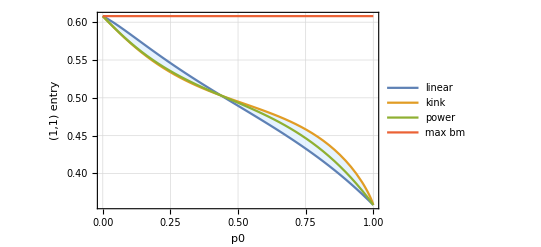

```mathematica
Plot[{Evaluate[FinalSigma[1,p0,-p0,wp[p0]][[1,1]]],
Evaluate[FinalSigma[1,p0,-p0-(1-p0)Log[1-p0],wp[p0]][[1,1]]],
Evaluate[FinalSigma[1,p0,-p0^2,wp[p0]][[1,1]]],
0.608},
{p0,0,1},PlotLegends->{"linear","kink","power","max bm"},AxesLabel->{"p0","(1,1) entry"},PlotRange->All,PlotTheme->"Detailed",
Filling->{1->{2}},FillingStyle->Directive[Opacity[0.75],LightBlue]]
```

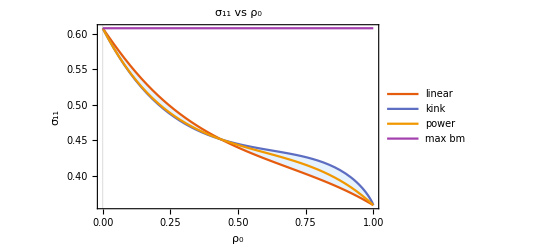

```mathematica
Plot[{Evaluate[FinalSigma[1,p0,-p0,wp[p0]]⟦1,1⟧],Evaluate[FinalSigma[1,p0,-p0-(1-p0) Log[1-p0],wp[p0]]⟦1,1⟧],Evaluate[FinalSigma[1,p0,-p0^2,wp[p0]]⟦1,1⟧],0.608},{p0,0,1},PlotTheme->"Scientific",PlotLegends->{"linear","kink","power","max bm"},AxesLabel->{"p0","(1,1) entry"},PlotLabel->TraditionalForm@Row[{Subscript[σ,11]," vs ",Subscript[ρ,0]}],LabelStyle->{16,Bold,FontFamily->"Times"},PlotRange->All,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.75],RGBColor[0.87,0.94,1]],FrameLabel->{TraditionalForm@Subscript[ρ,0],TraditionalForm@Subscript[σ,11] }]
```

```mathematica
Export["/home/erik/Downloads/var_alpha_corrected_nobc.pdf",Plot[{Evaluate[FinalSigma[1,p0,-p0,wp[p0]]⟦1,1⟧],Evaluate[FinalSigma[1,p0,-p0-(1-p0) Log[1-p0],wp[p0]]⟦1,1⟧],Evaluate[FinalSigma[1,p0,-p0^2,wp[p0]]⟦1,1⟧],0.608},{p0,0,1},PlotTheme->"Scientific",PlotLegends->{"linear","kink","power","max bm"},AxesLabel->{"p0","(1,1) entry"},PlotLabel->TraditionalForm@Row[{Subscript[σ,11]," vs ",Subscript[ρ,0]}],LabelStyle->{16,Bold,FontFamily->"Times"},PlotRange->All,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.75],RGBColor[0.87,0.94,1]],FrameLabel->{TraditionalForm@Subscript[ρ,0],TraditionalForm@Subscript[σ,11] }],"PDF"]
```

/home/erik/Downloads/var_alpha_corrected_nobc.pdf

```mathematica
Plot[{Evaluate[FinalSigma[1,p0,-p0,wp[p0]][[2,1]]],
Evaluate[FinalSigma[1,p0,-p0-(1-p0)Log[1-p0],wp[p0]][[2,1]]],
Evaluate[FinalSigma[1,p0,-p0^2,wp[p0]][[2,1]]],
-0.257},
{p0,0,1},PlotTheme->"Scientific",PlotLegends->{"linear","kink","power","max bm"},AxesLabel->{"p0","(1,1) entry"},PlotLabel->TraditionalForm@Row[{Subscript[σ,12]," vs ",Subscript[ρ,0]}],LabelStyle->{16,Bold,FontFamily->"Times"},PlotRange->All,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.75],RGBColor[0.87,0.94,1]],FrameLabel->{TraditionalForm@Subscript[ρ,0],TraditionalForm@Subscript[σ,12] }]
```

$Aborted

```mathematica
Export["/home/erik/Downloads/cov_alphasigma_corrected_nobc.pdf",Plot[{Evaluate[FinalSigma[1,p0,-p0,wp[p0]][[2,1]]],
Evaluate[FinalSigma[1,p0,-p0-(1-p0)Log[1-p0],wp[p0]][[2,1]]],
Evaluate[FinalSigma[1,p0,-p0^2,wp[p0]][[2,1]]],
-0.257},
{p0,0,1},PlotTheme->"Scientific",PlotLegends->{"linear","kink","power","max bm"},AxesLabel->{"p0","(1,1) entry"},PlotLabel->TraditionalForm@Row[{Subscript[σ,12]," vs ",Subscript[ρ,0]}],LabelStyle->{16,Bold,FontFamily->"Times"},PlotRange->All,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.75],RGBColor[0.87,0.94,1]],FrameLabel->{TraditionalForm@Subscript[ρ,0],TraditionalForm@Subscript[σ,12] }],"PDF"]
```

/home/erik/Downloads/cov_alphasigma_corrected_nobc.pdf

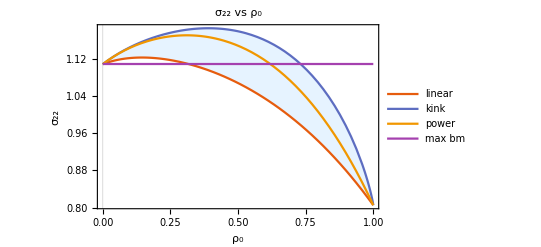

```mathematica
Plot[{Evaluate[FinalSigma[1,p0,-p0,wp[p0]][[2,2]]],
Evaluate[FinalSigma[1,p0,-p0-(1-p0)Log[1-p0],wp[p0]][[2,2]]],
Evaluate[FinalSigma[1,p0,-p0^2,wp[p0]][[2,2]]],1.109},
{p0,0,1},PlotTheme->"Scientific",PlotLegends->{"linear","kink","power","max bm"},AxesLabel->{"p0","(1,1) entry"},PlotLabel->TraditionalForm@Row[{Subscript[σ,22]," vs ",Subscript[ρ,0]}],LabelStyle->{16,Bold,FontFamily->"Times"},PlotRange->All,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.75],RGBColor[0.87,0.94,1]],FrameLabel->{TraditionalForm@Subscript[ρ,0],TraditionalForm@Subscript[σ,22] }]
```

```mathematica
Export["/home/erik/Downloads/var_sigma_corrected_nobc.pdf",Plot[{Evaluate[FinalSigma[1,p0,-p0,wp[p0]][[2,2]]],
Evaluate[FinalSigma[1,p0,-p0-(1-p0)Log[1-p0],wp[p0]][[2,2]]],
Evaluate[FinalSigma[1,p0,-p0^2,wp[p0]][[2,2]]],1.109},
{p0,0,1},PlotTheme->"Scientific",PlotLegends->{"linear","kink","power","max bm"},AxesLabel->{"p0","(1,1) entry"},PlotLabel->TraditionalForm@Row[{Subscript[σ,22]," vs ",Subscript[ρ,0]}],LabelStyle->{16,Bold,FontFamily->"Times"},PlotRange->All,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.75],RGBColor[0.87,0.94,1]],FrameLabel->{TraditionalForm@Subscript[ρ,0],TraditionalForm@Subscript[σ,22] }],"PDF"]
```

/home/erik/Downloads/var_sigma_corrected_nobc.pdf

```mathematica
plot11 := Plot[{Evaluate[FinalSigma[1,p0,-p0,wp[p0]][[1,1]]],Evaluate[FinalSigma[1,p0,-p0-(1-p0) Log[1-p0],wp[p0]][[1,1]]],Evaluate[FinalSigma[1,p0,-p0^2,wp[p0]][[1,1]]],0.608},{p0,0,1}]
```

```mathematica
plot12:=Plot[{Evaluate[FinalSigma[1,p0,-p0,wp[p0]][[1,2]]],Evaluate[FinalSigma[1,p0,-p0-(1-p0) Log[1-p0],wp[p0]][[1,2]]],Evaluate[FinalSigma[1,p0,-p0^2,wp[p0]][[1,2]]],-0.257},{p0,0,1}]
```

```mathematica
plot22:=Plot[{Evaluate[FinalSigma[1,p0,-p0,wp[p0]][[2,2]]],Evaluate[FinalSigma[1,p0,-p0-(1-p0) Log[1-p0],wp[p0]][[2,2]]],Evaluate[FinalSigma[1,p0,-p0^2,wp[p0]][[2,2]]],1.109},{p0,0,1}]
```

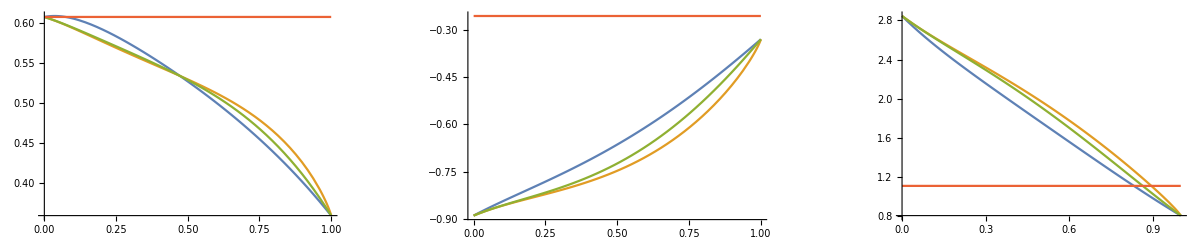

```mathematica
row=GraphicsRow[{plot11,plot12,plot22},Spacings->Scaled[.3]]
(*Legended[row,Placed[LineLegend[{"linear","kink","power","max bm"}],Below]]*)
```

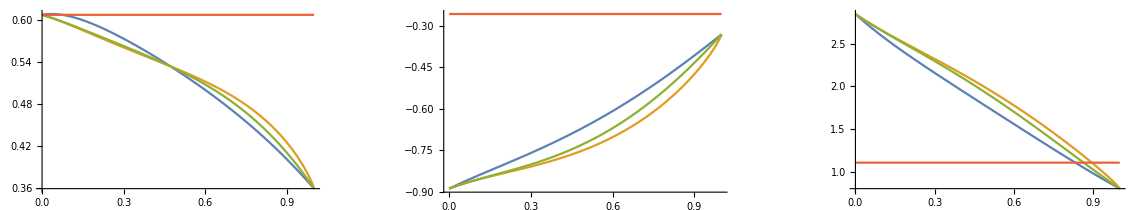

```mathematica
Show[row,ImageSize->{1138,210},AspectRatio->Full,PlotTheme->"Scientific",FrameLabel->{"p0","(1,1) entry"}]
```

```mathematica
Export["/home/erik/Downloads/var.pdf",%62,"PDF"]
```

/home/erik/Downloads/var.pdf

```mathematica
GraphicsRow[{Plot[{Evaluate[FinalSigma[1,p0,-p0,wp[p0]][[1,1]]],Evaluate[FinalSigma[1,p0,-p0-(1-p0) Log[1-p0],wp[p0]][[1,1]]],Evaluate[FinalSigma[1,p0,-p0^2,wp[p0]][[1,1]]],0.608},{p0,0,1},PlotLegends->None,AxesLabel->{"p0","(1,2) entry"},PlotRange->All,PlotTheme->"Detailed",Filling->{1->{2}},FillingStyle->Directive[Opacity[0.75],LightBlue]],Plot[{Evaluate[FinalSigma[1,p0,-p0,wp[p0]][[1,2]]],Evaluate[FinalSigma[1,p0,-p0-(1-p0) Log[1-p0],wp[p0]][[1,2]]],Evaluate[FinalSigma[1,p0,-p0^2,wp[p0]][[1,2]]],-0.257},{p0,0,1},AxesLabel->{"p0","(1,2) entry"},PlotRange->All,PlotTheme->"Detailed",Filling->{1->{2}},PlotLegends->None,FillingStyle->Directive[Opacity[0.75],LightBlue]],Plot[{Evaluate[FinalSigma[1,p0,-p0,wp[p0]][[2,2]]],Evaluate[FinalSigma[1,p0,-p0-(1-p0) Log[1-p0],wp[p0]][[2,2]]],Evaluate[FinalSigma[1,p0,-p0^2,wp[p0]][[2,2]]],1.109},{p0,0,1},AxesLabel->{"p0","(2,2) entry"},PlotRange->All,PlotTheme->"Detailed",PlotLegends->{"linear","kink","power","max bm"},AxesLabel->{"p0","(1,1) entry"},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.75],LightBlue]]}]
```

-Graphics-

```mathematica
Integrate[(p(1-x^(1/p))-p)/x,{x,0,1}]
```

ConditionalExpression[-p^2, Re[p]>0]

```mathematica
testp0=0.5
```

0.5

```mathematica
testp1=-testp0-(1-testp0)Log[1-testp0]
```

-0.153426

```mathematica
N[Sigma[1,testp0,testp1, wp[testp0]]//MatrixForm]
```

(4.71042 | -2.51753 | 1.64153 | 1.77091
-2.51753 | 1.46347 | -1.1617 | -1.25132
1.64153 | -1.1617 | 1.39493 | 1.49151
1.77091 | -1.25132 | 1.49151 | 1.64493)

```mathematica
N[Sigma[1,0,0, wp[0]]//MatrixForm]
```

(2.31418 | -1.42278 | 1.06772 | 0.
-1.42278 | 1. | -1. | 0.
1.06772 | -1. | 1.64493 | 1.64493
0. | 0. | 1.64493 | 1.64493)

```mathematica
N[Sigma[1,1,-1, wp[1]]//MatrixForm]
```

(7.7638 | -3.84557 | 1.71265 | 1.71265
-3.84557 | 2. | -1. | -1.
1.71265 | -1. | 0.644934 | 0.644934
1.71265 | -1. | 0.644934 | 1.64493)

#### Sanity checks

```mathematica
datalin=Table[{p0,FinalSigma[1,p0,-p0,wp[p0]][[1,1]]},{p0,0,1,0.05}]
```

{{0.,0.607927},{0.05,0.580894},{0.1,0.556102},{0.15,0.534046},{0.2,0.514686},{0.25,0.497785},{0.3,0.483042},{0.35,0.470151},{0.4,0.45882},{0.45,0.448779},{0.5,0.439778},{0.55,0.431584},{0.6,0.423976},{0.65,0.416742},{0.7,0.409673},{0.75,0.402559},{0.8,0.395187},{0.85,0.387333},{0.9,0.378761},{0.95,0.369221},{1.,0.35844}}

```mathematica
datakink=Table[{p0,FinalSigma[1,p0,-p0-(1-p0) Log[1-p0],wp[p0]][[1,1]]},{p0,0,1,0.05}]
```

{{0.,0.607927},{0.05,0.573813},{0.1,0.545239},{0.15,0.521653},{0.2,0.502366},{0.25,0.486717},{0.3,0.474117},{0.35,0.46405},{0.4,0.456063},{0.45,0.449752},{0.5,0.444741},{0.55,0.440674},{0.6,0.437191},{0.65,0.433915},{0.7,0.430428},{0.75,0.426246},{0.8,0.420772},{0.85,0.413222},{0.9,0.402459},{0.95,0.386504},{1.,Indeterminate}}

```mathematica
datapower=Table[{p0,FinalSigma[1,p0,-p0^2,wp[p0]][[1,1]]},{p0,0,1,0.05}]
```

{{0.,0.607927},{0.05,0.573991},{0.1,0.545792},{0.15,0.522608},{0.2,0.503644},{0.25,0.488167},{0.3,0.475535},{0.35,0.465194},{0.4,0.456661},{0.45,0.449511},{0.5,0.443358},{0.55,0.437845},{0.6,0.43263},{0.65,0.427375},{0.7,0.42174},{0.75,0.415374},{0.8,0.407905},{0.85,0.398933},{0.9,0.388024},{0.95,0.374702},{1.,0.35844}}

```mathematica
datalinsig=Table[{p0,FinalSigma[1,p0,-p0,wp[p0]][[2,2]]},{p0,0,1,0.05}]
```

{{0.,1.10866},{0.05,1.11732},{0.1,1.12176},{0.15,1.12292},{0.2,1.12137},{0.25,1.11747},{0.3,1.11146},{0.35,1.10346},{0.4,1.09355},{0.45,1.08174},{0.5,1.06801},{0.55,1.05232},{0.6,1.0346},{0.65,1.01474},{0.7,0.992656},{0.75,0.968208},{0.8,0.941261},{0.85,0.91166},{0.9,0.879241},{0.95,0.843825},{1.,0.805223}}

```mathematica
datakinksig=Table[{p0,FinalSigma[1,p0,-p0-(1-p0) Log[1-p0],wp[p0]][[2,2]]},{p0,0,1,0.05}]
```

{{0.,1.10866},{0.05,1.12873},{0.1,1.14491},{0.15,1.15797},{0.2,1.16835},{0.25,1.17629},{0.3,1.18189},{0.35,1.18513},{0.4,1.18592},{0.45,1.18409},{0.5,1.1794},{0.55,1.17153},{0.6,1.16009},{0.65,1.14457},{0.7,1.12435},{0.75,1.09859},{0.8,1.06622},{0.85,1.02565},{0.9,0.974415},{0.95,0.907714},{1.,Indeterminate}}

```mathematica
datapowersig=Table[{p0,FinalSigma[1,p0,-p0^2,wp[p0]][[2,2]]},{p0,0,1,0.05}]
```

{{0.,1.10866},{0.05,1.12845},{0.1,1.14373},{0.15,1.15527},{0.2,1.16348},{0.25,1.16859},{0.3,1.1707},{0.35,1.16982},{0.4,1.16588},{0.45,1.15878},{0.5,1.14836},{0.55,1.13443},{0.6,1.11677},{0.65,1.09513},{0.7,1.06922},{0.75,1.03875},{0.8,1.00337},{0.85,0.962732},{0.9,0.916441},{0.95,0.864085},{1.,0.805223}}

```mathematica
Plot[{Evaluate[FinalSigma[1,p0,-p0,wp[p0]][[1,1]]],Evaluate[FinalSigma[1,p0,-p0-(1-p0) Log[1-p0],wp[p0]][[1,1]]],Evaluate[FinalSigma[1,p0,-p0^2,wp[p0]][[1,1]]],0.608},{p0,0,1}]
```

```mathematica
N[Pi^2/3-1-EulerGamma]
```

1.71265

```mathematica
(3-12 p0^2+EulerGamma^2 (3+6 p0-3 p0^2)+6 EulerGamma (-2-5 p0+2 p0^2)+π^2+2 p0 (9+π^2))/(3 a^2)/.{a->1,p0->1}
```

1/3 (-9-30 EulerGamma+6 EulerGamma^2+π^2+2 (9+π^2))

```mathematica
N[2EulerGamma-5]
```

-3.84557

```mathematica
N[3-10EulerGamma+2EulerGamma^2+Pi^2]
```

7.7638

## The bias of the special case

```mathematica
Bf1[w_,p0_]:=1/2 Gamma[1+w] (1-2 (-6+(1-p0)) (1-p0)+4 w+2 (5-2 (1-p0)) (1-p0) w-3 (-1+(1-p0)) w^2+(-2 (1-p0)^2 w (1+w)+w (1+w)^2+(1-p0) (8+w (12-(-5+w) w))) PolyGamma[0,1+w])
```

```mathematica
Bf2[w_,p0_]:=1/2 w ((1-p0) ((-1+w) w+2 (1-p0) (1+w)) Gamma[1+w]-(1+w) Gamma[2+w])
```

```mathematica
Bf3[w_,p0_]:=1/2-(1-p0)^2
```

```mathematica
Bf4[w_,p0_]:=1/2+(1-p0)
```

```mathematica
B[n_,r_,w_,p0_]:=(1/r)*Mbc[1,p0,w].M[1,p0,w].{Bf1[w,p0],Bf2[w,p0],Bf3[w,p0],Bf4[w,p0]}
```

```mathematica
V[n_,r_,w_,p0_]:=(r/n)*FinalSigma[1,p0,-p0,w][[1,1]]
```

```mathematica
Vmax[n_,r_,w_,p0_]:=(r/n)*FinalSigma[1,p0,-p0-(1-p0)Log[1-p0],w][[1,1]]
```

```mathematica
V[1000,100,wp[.5],.5]+B[1000,100,wp[.5],.5][[1]]^2
```

0.0540555

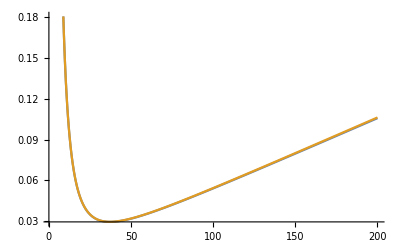

```mathematica
Plot[{V[1000,r,wp[.5],.5]+B[1000,r,wp[.5],.5][[1]]^2,
Vmax[1000,r,wp[.5],.5]+B[1000,r,wp[.5],.5][[1]]^2},{r,1,200}]
```

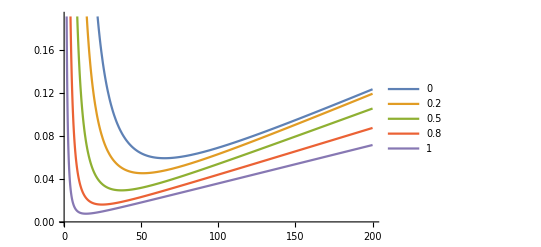

```mathematica
Plot[{V[1000,r,wp[.0],.0]+B[1000,r,wp[.0],.0][[1]]^2,
V[1000,r,wp[.2],.2]+B[1000,r,wp[.2],.2][[1]]^2,
V[1000,r,wp[.5],.5]+B[1000,r,wp[.5],.5][[1]]^2,
V[1000,r,wp[.8],.8]+B[1000,r,wp[.8],.8][[1]]^2,
V[1000,r,wp[1],1]+B[1000,r,wp[1],1][[1]]^2},{r,1,200},PlotLegends->{0,.2,.5,.8,1}]
```

## New Attempt

```mathematica
G[x_,a_]:=Exp[-x^(-a)]
```

```mathematica
Gy[x_,a_, ρ_]:=Exp[-x^(-a)](1+ρ[0]*x^(-a))
```

```mathematica
H[x_,y_,a_,ρ_]:=G[y,a]*(1+ρ[(y/x)^a]*y^(-a))
```

```mathematica
H[x,y,a,ρ]
```

ⅇ^(-y^-a) (1+y^-a ρ[(y/x)^a])

```mathematica
ρiid[x_]:=Piecewise[{{1-x,0<x<1}}]
```

```mathematica
ρiid[x_]:=(1-x^2)/2
```

```mathematica
f[y_,a_]:=Log[y]
```

```mathematica
Integrate[(H[x,y,a,ρiid]-G[x,a]Gy[y,a, ρiid])*(D[f[y,a],y]/x),{y,0,x},Assumptions->a>0&&x>0]+G[x,a]*Integrate[(1-Gy[y,a, ρiid])*(D[f[y,a],y]/x),{y,x,Infinity},Assumptions->a>0&&x>0]
```

(ⅇ^(-2 x^-a) (-1+ⅇ^(x^-a) (1-x^-a))+(2-2 ⅇ^(-x^-a)+x^(-2 a)) ExpIntegralE[1,x^-a])/(2 a x)+(ⅇ^(-x^-a) (-1+ⅇ^(-x^-a)+2 EulerGamma-2 ExpIntegralEi[-x^-a]-2 a Log[x]))/(2 a x)

```mathematica
FullSimplify[(ⅇ^(-2 x^-a) (-1+ⅇ^(x^-a))+(-1+ⅇ^(-x^-a)+x^-a) ExpIntegralEi[-x^-a])/(a x)+(ⅇ^(-x^-a) (-1+ⅇ^(-x^-a)+EulerGamma-ExpIntegralEi[-x^-a]-a Log[x]))/(a x)]
```

((-1+x^-a) ExpIntegralEi[-x^-a]+ⅇ^(-x^-a) (EulerGamma-a Log[x]))/(a x)

```mathematica
Integrate[(ⅇ^(-2 x^-a) (-1+ⅇ^(x^-a) (1-x^-a))+(2-2 ⅇ^(-x^-a)+x^(-2 a)) ExpIntegralE[1,x^-a])/(2 a x)+(ⅇ^(-x^-a) (-1+ⅇ^(-x^-a)+2 EulerGamma-2 ExpIntegralEi[-x^-a]-2 a Log[x]))/(2 a x),{x,0,Infinity},Assumptions->a>0]
```

Integrate[(ⅇ^(-2 x^-a) (-1+ⅇ^(x^-a) (1-x^-a))+(2-2 ⅇ^(-x^-a)+x^(-2 a)) ExpIntegralE[1,x^-a])/(2 a x)+(ⅇ^(-x^-a) (-1+ⅇ^(-x^-a)+2 EulerGamma-2 ExpIntegralEi[-x^-a]-2 a Log[x]))/(2 a x),{x,0,∞},Assumptions→a>0]

```mathematica
Integrate[(H[x,y,a,ρ]-G[x,a]Gy[y,a, ρ])*(D[f[y,a],y]/x),{y,0,x},Assumptions->a>0&&x>0]+G[x,a]*Integrate[(1-Gy[y,a, ρ])*(D[f[y,a],y]/x),{y,x,Infinity},Assumptions->a>0&&x>0]
```

Integrate[(-ⅇ^(-x^-a-y^-a) (1+y^-a ρ[0])+ⅇ^(-y^-a) (1+y^-a ρ[(y/x)^a]))/(x y),{y,0,x},Assumptions→a>0&&x>0]-(ⅇ^(-x^-a) (-EulerGamma+ExpIntegralEi[-x^-a]+a Log[x]+ρ[0]-ⅇ^(-x^-a) ρ[0]))/(a x)

## Schmier

```mathematica
Integrate[y^(-a)Exp[-y^(-a)]/y,{y,0,Infinity},Assumptions->a>0]
```

1/a

```mathematica
Integrate[y^(-a)Exp[-y^(-a)]*(-a)*y^(-a-1),{y,0,Infinity},Assumptions->a>0]
```

-1

```mathematica
Integrate[y^(-a)Exp[-y^(-a)]*D[y^(-a)Log[y],y],{y,0,Infinity},Assumptions->a>0]
```

(2-EulerGamma)/a

```mathematica
Integrate[Exp[-y^(-a)]/y,{y,0,Infinity},Assumptions->a>0]
```

Integrate::idiv: Integral of (ⅇ^(-y^-a))/y does not converge on {0,∞}.

Integrate[(ⅇ^(-y^-a))/y,{y,0,∞},Assumptions→a>0]

```mathematica
z=.
```

```mathematica
Integrate[(Exp[-x^(-a)/z]*z^(-2)*(1-z)*x^(-a)-Exp[-x^(-a)])/x,{z,0,1},Assumptions->a>0&&x>0]
```

-x^(-1-a) Gamma[0,x^-a]

```mathematica
Integrate[-x^(-1-a) Gamma[0,x^-a],{x,0,∞},Assumptions->a>0]
```

-1/a

```mathematica
Integrate[(1-z)*Exp[-x^(-a)/z]*z^(-2)*x^(-a),{z,0,1},Assumptions->a>0&&x>0]
```

ⅇ^(-x^-a)-x^-a Gamma[0,x^-a]

```mathematica
Integrate[-x^-a Gamma[0,x^-a]/x,{x,0,Infinity},Assumptions->a>0&&x>0]
```

-1/a

```mathematica
Integrate[Exp[-x^(-a)/z]*z^(-2)*x^(-a),{z,0,1-p},Assumptions->a>0&&x>0&&0<p<1]
```

ⅇ^(x^-a/(-1+p))

```mathematica
Integrate[(1-z)/p*Exp[-x^(-a)/z]*z^(-2)*x^(-a),{z,1-p,1},Assumptions->a>0&&x>0&&0<p<1]
```

(-ⅇ^(-x^-a) (-1+ⅇ^((p x^-a)/(-1+p)))+x^-a (-Gamma[0,x^-a]+Gamma[0,-x^-a/(-1+p)]))/p

```mathematica
FullSimplify[(-ⅇ^(-x^-a) (-1+ⅇ^((p x^-a)/(-1+p)))+x^-a (-Gamma[0,x^-a]+Gamma[0,-x^-a/(-1+p)]))/p+ⅇ^(x^-a/(-1+p))]
```

(ⅇ^(-x^-a) (1+ⅇ^((p x^-a)/(-1+p)) (-1+p))+x^-a (-Gamma[0,x^-a]+Gamma[0,-x^-a/(-1+p)]))/p

```mathematica
p=.
```

```mathematica
Integrate[((ⅇ^(-x^-a) (1+ⅇ^((p x^-a)/(-1+p)) (-1+p))+x^-a (-Gamma[0,x^-a]+Gamma[0,-x^-a/(-1+p)]))/p-Exp[-x^(-a)])/x,{x,0,∞},Assumptions->a>0&&0<p<1]
```

(-p+(-1+p) Log[1-p])/(a p)

```mathematica
Integrate[x^(-a-1)(Exp[-x^(-a)/z]),{x,0,Infinity},Assumptions->a>0&&z>0]
```

z/a

```mathematica
Integrate[Gamma[0,x^-a]/x,{x,0,Infinity},Assumptions->a>0]
```

Integrate::idiv: Integral of Gamma[0,x^-a]/x does not converge on {0,∞}.

Integrate[Gamma[0,x^-a]/x,{x,0,∞},Assumptions→a>0]

```mathematica
Integrate[(ⅇ^(-x^-a/z)-ⅇ^(-x^-a))/x,{x,0,Infinity},Assumptions->a>0&&z>0]
```

Log[z]/a

```mathematica
D[Exp[-x^(-a)/z](1+x^(-a)/z)Log[x^(-a)/z]+Gamma[0,x^(-a)/z]+Exp[-x^(-a)/z],z]//FullSimplify
```

(ⅇ^(-x^-a/z) x^(-2 a) Log[x^-a/z])/z^3

```mathematica
Integrate[Exp[-x^(-a)/z](1+x^(-a)/z)Log[x^(-a)/z]+Gamma[0,x^(-a)/z]+Exp[-x^(-a)/z],{z,0,1},Assumptions->a>0&&x>0]
```

(-1+x^-a) ExpIntegralEi[-x^-a]+ⅇ^(-x^-a) (1-a Log[x])

```mathematica
Integrate[(Exp[-x^(-a)/z](1+x^(-a)/z)Log[x^(-a)/z]+Gamma[0,x^(-a)/z]+Exp[-x^(-a)/z]-((-1+x^-a) ExpIntegralEi[-x^-a]+ⅇ^(-x^-a) (1-a Log[x])))/x,{x,0,Infinity},Assumptions->a>0&&z>0]
```

-((-1+EulerGamma) (1+Log[z]))/a

```mathematica
Integrate[(x^-a ExpIntegralEi[-x^-a])/x,{x,0,Infinity},Assumptions->a>0]
```

-1/a

```mathematica
Integrate[(ⅇ^(-x^-a) (1-EulerGamma-a Log[x]))/x,{x,0,Infinity},Assumptions->a>0]
```

Integrate::idiv: Integral of -(ⅇ^(-x^-a) (-1+EulerGamma+a Log[x]))/x does not converge on {0,∞}.

```mathematica
Integrate[(ExpIntegralEi[-x^-a]-ⅇ^(-x^-a)EulerGamma)/x,{x,0,Infinity},Assumptions->a>0]
```

Integrate::idiv: Integral of -(ⅇ^(-x^-a) EulerGamma)/x+ExpIntegralEi[-x^-a]/x does not converge on {0,∞}.

Integrate[(-ⅇ^(-x^-a) EulerGamma+ExpIntegralEi[-x^-a])/x,{x,0,∞},Assumptions→a>0]

```mathematica
Integrate[((-1+x^-a) ExpIntegralEi[-x^-a]+ⅇ^(-x^-a) (1-a Log[x])+Gamma[0,x^(-a)]+(2-EulerGamma)Exp[-x^(-a)])/x,{x,0,Infinity},Assumptions->a>0]
```

```mathematica
Integrate[ⅇ^(-x^-a) x^(-a)D[x^(-a)Log[x],x],{x,0,Infinity},Assumptions->a>0]
```

(2-EulerGamma)/a

```mathematica
Limit[Exp[-x^(-a)/Abs[z]](1+x^(-a)/Abs[z])Log[x^(-a)/Abs[z]]+Gamma[0,x^(-a)/Abs[z]]+Exp[-x^(-a)/Abs[z]],z->0,Assumptions->x>0&&a>0]
```

0

```mathematica
Integrate[(ExpIntegralEi[-x^(-a)](x^(-a)-1)+(EulerGamma-a Log[x])Exp[-x^(-a)])/x,{x,0,Infinity},Assumptions->a>0]
```

(-6+π^2)/(6 a)

## noch mehr schmier

```mathematica
Limit[Exp[-x/Abs[z]](1+x/Abs[z]),z->1, Assumptions->x>0]
```

ⅇ^-x (1+x)

```mathematica
Integrate[Exp[-y^(-a)/z]y^(-a)/y,{y,0,Infinity},Assumptions->a>0&&z>0]
```

z/a

```mathematica
Integrate[Exp[-y^(-a)]y^(-a)*D[y^(-a*w),y],{y,0,Infinity},Assumptions->a>0&&1>w>0]
```

-w Gamma[1+w]

```mathematica
Integrate[Exp[-y^(-a)]y^(-a)*D[y^(-a*w)Log[y],y],{y,0,Infinity},Assumptions->a>0&&1>w>0]
```

(Gamma[1+w] (1+w PolyGamma[0,1+w]))/a

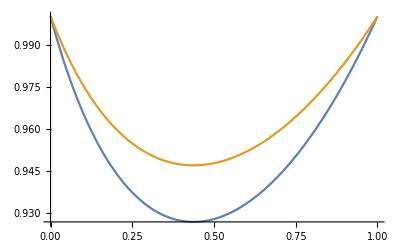

```mathematica
Plot[{wp[ppp] Gamma[1+wp[ppp]],wp[ppp]},{ppp,0,1}]
```